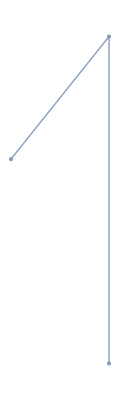

```mathematica
a={-0.02, 0.05};
b={0.1, 0.2};
c={0.1, -0.2};
one=Graphics[{
Line[{a,b,c}]
}];
DiscretizeGraphics[one]
```

0.1

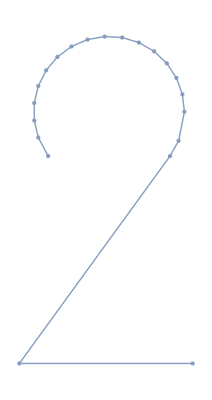

{{0.18,0.05},{0.177304,0.0730616},{0.169363,0.0948799},{0.156604,0.114279},{0.139716,0.130212},{0.119608,0.141822},{0.0973648,0.148481},{0.0741855,0.149831},{0.0513197,0.145799},{0.03,0.136603},{0.0113758,0.122737},{-0.00354878,0.104951},{-0.0139693,0.084202},{-0.0193238,0.0616093},{-0.0193238,0.0383907},{-0.0139693,0.015798},{-0.000901699,-0.00877853},{0.160902,-0.00877853},{0.172276,0.0114631},{-0.0390983,-0.284055},{0.190902,-0.284055}}

```mathematica
a={-0.02, 0.05};
b={0.1, 0.2};
c={0.1, -0.2};
r=0.1
fi=Pi/5;
center=a+{r,0};
neckLength=0.2;
two=Graphics[{
Circle[center, r,{0, Pi+fi}],
Circle[center, r,{2*Pi-fi, 2*Pi}],
Line[{center+r*{Cos[-fi], Sin[-fi]},center+r*{Cos[-fi], Sin[-fi]}+{-neckLength,-neckLength*Tan[Pi/2-fi]}}],
Line[{center+r*{Cos[-fi], Sin[-fi]}+{-neckLength,-neckLength*Tan[Pi/2-fi]},center+r*{Cos[-fi], Sin[-fi]}+{-neckLength,-neckLength*Tan[Pi/2-fi]}+{0.23,0}}]
}];
DiscretizeGraphics[two]
coords=MeshCoordinates[DiscretizeGraphics[two]];
coords=Flatten[MeshPrimitives[DiscretizeGraphics[two],1]/.Line[u_]->u, 1]//DeleteDuplicates
```

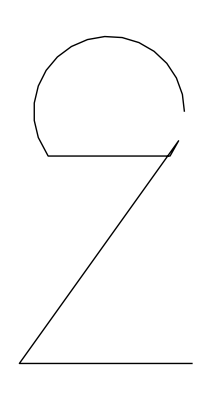

```mathematica
Graphics[Line[coords]]
```